```mathematica
diffEq=D[ψ[x,t],t]==𝒟 D[ψ[x,t],{x,2}]
```

ψ^(0,1)[x,t]==𝒟 ψ^(2,0)[x,t]

```mathematica
ψ0[x_]:=1-x
```

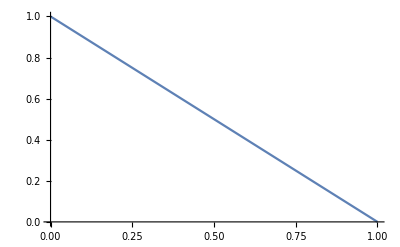

```mathematica
Plot[ψ0[x],{x,0,1}]
```

```mathematica
bc0=ψ[0,t]==1
```

ψ[0,t]==1

```mathematica
bc1=ψ[1,t]==0
```

ψ[1,t]==0

```mathematica
bc2=ψ[x,0]==ψ0[x]
```

ψ[x,0]==1-x

```mathematica
sol=DSolve[{diffEq,bc0,bc1,bc2},ψ[x,t],{x,t}]
```

{{ψ[x,t]→1-x}}

```mathematica
f[x_,t_,𝒟_]:=1-x
```

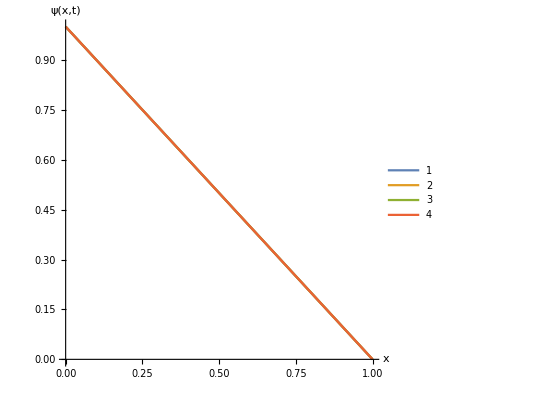

```mathematica
Plot[{f[x,0,0.1],f[x,1/9,0.1],f[x,2/9,0.1],f[x,3/9,0.1]},{x,0,1},PlotRange->{0,1},AxesLabel->{"x","ψ(x,t)"},PlotLegends->Automatic,AspectRatio->1]
```